```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
dark801 = Delete[Import["E:\Google Drive\Advanced_Lab\Matt Project\80dark1.txt","table"],{1}] ;
light803 = Delete[Import["E:\Google Drive\Advanced_Lab\Matt Project\80light3.txt","table"],{1}] ;
dark1341=Delete[Import["E:\Google Drive\Advanced_Lab\Matt Project\dark134.csv","csv"],{1}];
light1341=Delete[Import["E:\Google Drive\Advanced_Lab\Matt Project\light134.csv","csv"],{1}];
dark1881=Delete[Import["E:\Google Drive\Advanced_Lab\Matt Project\188dark1.txt","table"],{1}];
light1881=Delete[Import["E:\Google Drive\Advanced_Lab\Matt Project\188light1.txt","table"],{1}];
dark2421=Delete[Import["E:\Google Drive\Advanced_Lab\Matt Project\dark242.csv","csv"],{1}];
light2421=Delete[Import["E:\Google Drive\Advanced_Lab\Matt Project\light242.csv","csv"],{1}];
dark2961=Delete[Import["E:\Google Drive\Advanced_Lab\Matt Project\296dark1.txt","table"],{1}];
light2961=Delete[Import["E:\Google Drive\Advanced_Lab\Matt Project\296light2.txt","table"],1];
```

```mathematica
power80=Delete[Import["E:\Google Drive\Advanced_Lab\Matt Project\power80.csv","csv"],{1}];
power134=Delete[Import["E:\Google Drive\Advanced_Lab\Matt Project\power134.csv","csv"],{1}];
power188=Delete[Import["E:\Google Drive\Advanced_Lab\Matt Project\power188.csv","csv"],{1}];
power242=Delete[Import["E:\Google Drive\Advanced_Lab\Matt Project\power242.csv","csv"],{1}];
power296=Delete[Import["E:\Google Drive\Advanced_Lab\Matt Project\power296.csv","csv"],{1}];
```

```mathematica
{m1,m2,m3,m4}=Graphics/@{Circle[{0,0},1],Disk[{0,0},1],Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}],Polygon[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5}}]};
```

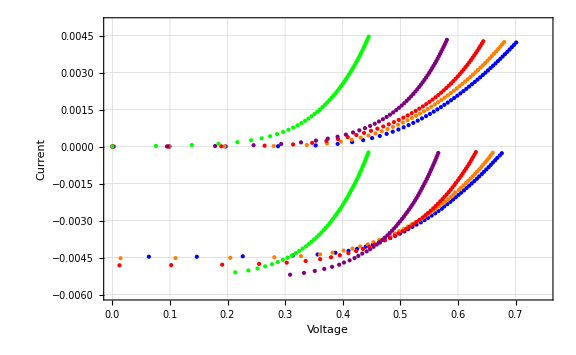

```mathematica
dataplot = ListPlot[{dark801, light803[[1;;55]],dark1341,light1341[[1;;55]],dark1881, light1881[[1;;55]],dark2421,light2421[[1;;54]],dark2961,light2961[[1;;53]]}, ImageSize -> Large, Frame -> True, FrameLabel -> {"Voltage","Current"}, GridLines-> Automatic, GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{0,.75},{-.006,.005}},PlotStyle -> {Blue,Blue,Orange,Orange, Red,Red,Purple,Purple,Green,Green}]
```

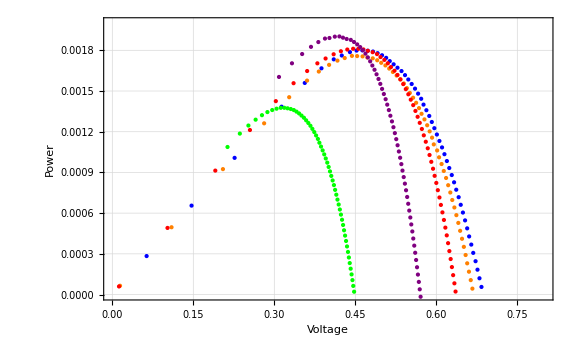

```mathematica
powerplot = ListPlot[{power80,power134,power188,power242,power296}, ImageSize -> Large, Frame -> True, FrameLabel -> {"Voltage","Power"}, GridLines-> Automatic, GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{0,.8},{0,.002}},PlotStyle -> {Blue,Orange,Red,Purple,Green}]
```

```mathematica
Il=0;
```

```mathematica
Rs=44;Rsh=47500;T=80;Io = 3 * 10^-35;n=1;dark80fit = -(1/(Rs (1. Rs+1. Rsh))(1. Il Rs Rsh-1. Rs V+n (-0.00008625000000000001 Rs-0.00008625000000000001 Rsh) T ProductLog[(11594.202898550724 ⅇ^((11594.202898550724 Il Rs Rsh+11594.202898550724 Rsh V)/(n Rs T+n Rsh T)) Io Rs Rsh)/(1. n Rs T+1. n Rsh T)]));
```

```mathematica
Rs=36;Rsh=29252;T=188;Io=3*10^-16;n=1;dark188fit = -(1/(Rs (1. Rs+1. Rsh))(1. Il Rs Rsh-1. Rs V+n (-0.00008625000000000001 Rs-0.00008625000000000001 Rsh) T ProductLog[(11594.202898550724 ⅇ^((11594.202898550724 Il Rs Rsh+11594.202898550724 Rsh V)/(n Rs T+n Rsh T)) Io Rs Rsh)/(1. n Rs T+1. n Rsh T)]));
```

```mathematica
Rs=29;Rsh=7519;T=296;Io=1.2*10^-8;n=1;dark296fit = -(1/(Rs (1. Rs+1. Rsh))(1. Il Rs Rsh-1. Rs V+n (-0.00008625000000000001 Rs-0.00008625000000000001 Rsh) T ProductLog[(11594.202898550724 ⅇ^((11594.202898550724 Il Rs Rsh+11594.202898550724 Rsh V)/(n Rs T+n Rsh T)) Io Rs Rsh)/(1. n Rs T+1. n Rsh T)]));
```

```mathematica
Rs=41;Rsh=59667;T=134;Io=3*10^-22;n=1;dark134fit = -(1/(Rs (1. Rs+1. Rsh))(1. Il Rs Rsh-1. Rs V+n (-0.00008625000000000001 Rs-0.00008625000000000001 Rsh) T ProductLog[(11594.202898550724 ⅇ^((11594.202898550724 Il Rs Rsh+11594.202898550724 Rsh V)/(n Rs T+n Rsh T)) Io Rs Rsh)/(1. n Rs T+1. n Rsh T)]));
```

```mathematica
Rs=28;Rsh=21769;T=242;Io=8*10^-13;n=1;dark242fit = -(1/(Rs (1. Rs+1. Rsh))(1. Il Rs Rsh-1. Rs V+n (-0.00008625000000000001 Rs-0.00008625000000000001 Rsh) T ProductLog[(11594.202898550724 ⅇ^((11594.202898550724 Il Rs Rsh+11594.202898550724 Rsh V)/(n Rs T+n Rsh T)) Io Rs Rsh)/(1. n Rs T+1. n Rsh T)]));
```

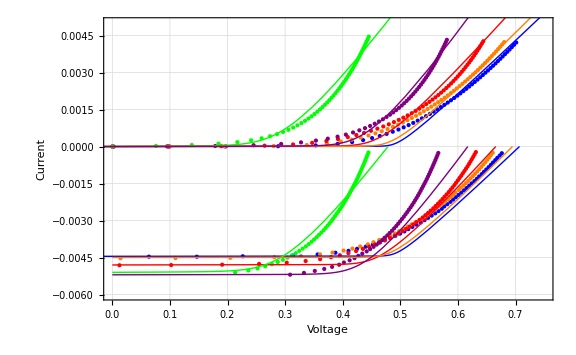

```mathematica
Show[dataplot,Plot[dark80fit,{V,-1,1},PlotRange-> {-.005,.006},PlotStyle -> {Blue,Thick}],Plot[dark80fit - 0.00445,{V,-1,1},PlotRange-> {-.005,0},PlotStyle -> {Blue,Thick}],Plot[dark188fit,{V,-1,1},PlotRange-> {-.005,.006},PlotStyle -> {Red,Thick}],Plot[dark188fit - 0.0048,{V,0,1},PlotRange-> {-.005,0},PlotStyle -> {Red,Thick}],Plot[dark296fit,{V,-1,1},PlotRange-> {-.005,.006},PlotStyle -> {Green,Thick}],Plot[dark296fit - 0.0051,{V,0,1},PlotRange-> {-.006,0},PlotStyle -> {Green,Thick}],Plot[dark134fit,{V,-1,1},PlotRange-> {-.005,.006},PlotStyle -> {Orange,Thick}],Plot[dark134fit - 0.0045,{V,0,1},PlotRange-> {-.006,.0},PlotStyle -> {Orange,Thick}],Plot[dark242fit,{V,-1,1},PlotRange-> {-.005,.006},PlotStyle -> {Purple,Thick}],Plot[dark242fit - 0.0052,{V,0,1},PlotRange-> {-.006,0},PlotStyle -> {Purple,Thick}]]
```

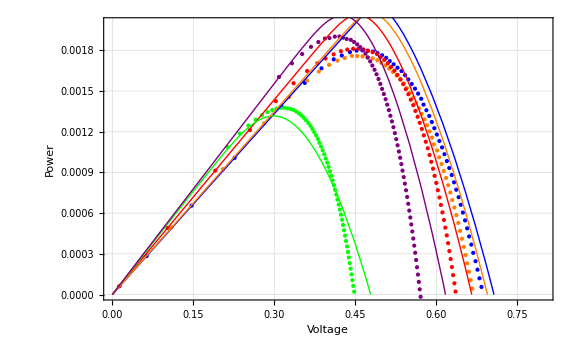

```mathematica
Show[powerplot, Plot[-V(dark80fit - 0.00445),{V,0,1},PlotRange-> {0,0.003},PlotStyle -> {Blue,Thick}],Plot[-V(dark188fit - 0.0048),{V,0,1},PlotRange-> {0,0.003},PlotStyle -> {Red,Thick}],Plot[-V(dark296fit - 0.0051),{V,0,1},PlotRange-> {0,0.003},PlotStyle -> {Green,Thick}],Plot[-V(dark134fit - 0.0045),{V,0,1},PlotRange->{0,0.003},PlotStyle -> {Orange,Thick}],
Plot[-V(dark242fit - 0.0052),{V,0,1},PlotRange-> {0,0.003},PlotStyle -> {Purple,Thick}]]
```

```mathematica
Rs=9;Rsh=7519;T=296;Io=1.7*10^-6;n=2;dark296fit = -(1/(Rs (1. Rs+1. Rsh))(1. Il Rs Rsh-1. Rs V+n (-0.00008625000000000001 Rs-0.00008625000000000001 Rsh) T ProductLog[(11594.202898550724 ⅇ^((11594.202898550724 Il Rs Rsh+11594.202898550724 Rsh V)/(n Rs T+n Rsh T)) Io Rs Rsh)/(1. n Rs T+1. n Rsh T)]));
```

```mathematica
Rs=40;Rsh=59667;T=134;Io=7*10^-12;n=2;dark134fit = -(1/(Rs (1. Rs+1. Rsh))(1. Il Rs Rsh-1. Rs V+n (-0.00008625000000000001 Rs-0.00008625000000000001 Rsh) T ProductLog[(11594.202898550724 ⅇ^((11594.202898550724 Il Rs Rsh+11594.202898550724 Rsh V)/(n Rs T+n Rsh T)) Io Rs Rsh)/(1. n Rs T+1. n Rsh T)]));
```

```mathematica
Rs=60;Rsh=47500;T=80;Io = 2* 10^-17;n=2;dark80fit = -(1/(Rs (1. Rs+1. Rsh))(1. Il Rs Rsh-1. Rs V+n (-0.00008625000000000001 Rs-0.00008625000000000001 Rsh) T ProductLog[(11594.202898550724 ⅇ^((11594.202898550724 Il Rs Rsh+11594.202898550724 Rsh V)/(n Rs T+n Rsh T)) Io Rs Rsh)/(1. n Rs T+1. n Rsh T)]));
```

```mathematica
Rs=30;Rsh=29252;T=188;Io=1.6*10^-9;n=2;dark188fit = -(1/(Rs (1. Rs+1. Rsh))(1. Il Rs Rsh-1. Rs V+n (-0.00008625000000000001 Rs-0.00008625000000000001 Rsh) T ProductLog[(11594.202898550724 ⅇ^((11594.202898550724 Il Rs Rsh+11594.202898550724 Rsh V)/(n Rs T+n Rsh T)) Io Rs Rsh)/(1. n Rs T+1. n Rsh T)]));
```

```mathematica
Rs=15;Rsh=21769;T=242;Io=3.5*10^-8;n=2;dark242fit = -(1/(Rs (1. Rs+1. Rsh))(1. Il Rs Rsh-1. Rs V+n (-0.00008625000000000001 Rs-0.00008625000000000001 Rsh) T ProductLog[(11594.202898550724 ⅇ^((11594.202898550724 Il Rs Rsh+11594.202898550724 Rsh V)/(n Rs T+n Rsh T)) Io Rs Rsh)/(1. n Rs T+1. n Rsh T)]));
```

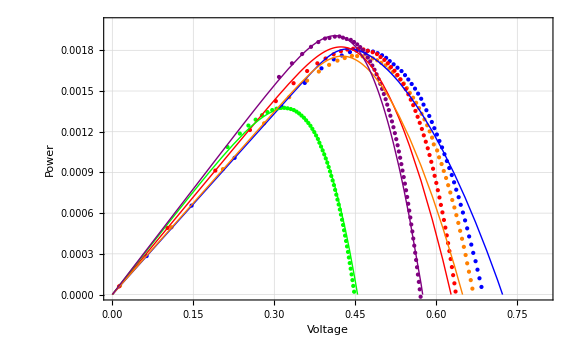

```mathematica
Show[powerplot, Plot[-V(dark80fit - 0.00445),{V,0,1},PlotRange-> {0,0.003},PlotStyle -> {Blue,Thick}],Plot[-V(dark188fit - 0.0048),{V,0,1},PlotRange-> {0,0.003},PlotStyle -> {Red,Thick}],Plot[-V(dark296fit - 0.0051),{V,0,1},PlotRange-> {0,0.003},PlotStyle -> {Green,Thick}],Plot[-V(dark134fit - 0.0045),{V,0,1},PlotRange->{0,0.003},PlotStyle -> {Orange,Thick}],
Plot[-V(dark242fit - 0.0052),{V,0,1},PlotRange-> {0,0.003},PlotStyle -> {Purple,Thick}]]
```

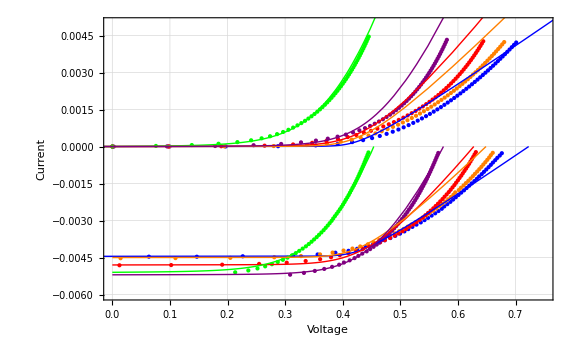

```mathematica
Show[dataplot,Plot[dark80fit,{V,-1,1},PlotRange-> {-.005,.006},PlotStyle -> {Blue,Thick}],Plot[dark80fit - 0.00445,{V,-1,1},PlotRange-> {-.005,0},PlotStyle -> {Blue,Thick}],Plot[dark188fit,{V,-1,1},PlotRange-> {-.005,.006},PlotStyle -> {Red,Thick}],Plot[dark188fit - 0.0048,{V,0,1},PlotRange-> {-.005,0},PlotStyle -> {Red,Thick}],Plot[dark296fit,{V,-1,1},PlotRange-> {-.005,.006},PlotStyle -> {Green,Thick}],Plot[dark296fit - 0.0051,{V,0,1},PlotRange-> {-.006,0},PlotStyle -> {Green,Thick}],Plot[dark134fit,{V,-1,1},PlotRange-> {-.005,.006},PlotStyle -> {Orange,Thick}],Plot[dark134fit - 0.0045,{V,0,1},PlotRange-> {-.006,.0},PlotStyle -> {Orange,Thick}],Plot[dark242fit,{V,-1,1},PlotRange-> {-.005,.006},PlotStyle -> {Purple,Thick}],Plot[dark242fit - 0.0052,{V,0,1},PlotRange-> {-.006,0},PlotStyle -> {Purple,Thick}]]
```

```mathematica
Rs=44;Rsh=47500;T=80;Il=0
dark80fit = NonlinearModelFit[dark801,{-(1/(Rs (1. Rs+1. Rsh))(1. Il Rs Rsh-1. Rs V+n (-0.00008625000000000001 Rs-0.00008625000000000001 Rsh) T ProductLog[(11594.202898550724 ⅇ^((11594.202898550724 Il Rs Rsh+11594.202898550724 Rsh V)/(n Rs T+n Rsh T)) Io Rs Rsh)/(1. n Rs T+1. n Rsh T)])), {Io >10^-70, n>1,  n<5}},{{Io,10^-20},n},V]
```

0

NonlinearModelFit::fdssnv: Search specification 2 without variables should be a list with 1 to 4 elements.

NonlinearModelFit[{{-4.67426,-0.000365317},{-4.64123,-0.000260058},{-4.58691,-0.00021134},{-4.52082,-0.000176612},{-4.44722,-0.000150512},{-4.36798,-0.000129611},{-4.28538,-0.000112586},{-4.19933,-0.0000985432},{-4.11107,-0.000086985},{-4.02044,-0.0000776187},{-3.92836,-0.0000699733},{-3.83459,-0.0000638303},{-3.7402,-0.0000585388},{-3.64452,-0.000054127},{-3.54849,-0.0000504021},{-3.45169,-0.0000470296},{-3.35491,-0.0000441021},{-3.25739,-0.0000415426},{-3.15991,-0.0000392068},{-3.06203,-0.0000370253},{-2.96425,-0.0000349957},{-2.86596,-0.0000331203},{-2.76784,-0.0000314019},{-2.6694,-0.0000297916},{-2.57114,-0.000028261},{-2.47249,-0.0000267304},{-2.37412,-0.0000253155},{-2.27531,-0.000023947},{-2.17681,-0.0000227431},{-2.07784,-0.0000214311},{-1.97918,-0.0000204073},{-1.88015,-0.000019278},{-1.78131,-0.0000182233},{-1.68223,-0.0000171506},{-1.58336,-0.0000162167},{-1.48424,-0.0000152495},{-1.38537,-0.0000141768},{-1.28619,-0.000013315},{-1.1873,-0.0000122706},{-1.08817,-0.0000114114},{-0.989272,-0.0000104081},{-0.890169,-9.4306×10^-6},{-0.791312,-8.3553×10^-6},{-0.692225,-7.3752×10^-6},{-0.593452,-6.3694×10^-6},{-0.494376,-5.2555×10^-6},{-0.395629,-4.2163×10^-6},{-0.296617,-3.1487×10^-6},{-0.197853,-1.9885×10^-6},{-0.0987365,-1.0238×10^-6},{-0.000049876,-4.63×10^-8},{0.0991877,9.518×10^-7},{0.196729,3.1461×10^-6},{0.287747,0.000012178},{0.353042,0.0000460238},{0.391189,0.000106736},{0.416312,0.000179971},{0.435396,0.000259435},{0.451007,0.000342296},{0.464362,0.000427136},{0.476203,0.000513683},{0.486868,0.000601103},{0.496697,0.00068973},{0.505807,0.000778683},{0.514379,0.000868431},{0.522465,0.000958456},{0.530184,0.00104904},{0.537541,0.00113975},{0.544607,0.00123107},{0.551387,0.00132226},{0.557974,0.00141407},{0.564311,0.00150573},{0.570482,0.00159786},{0.576459,0.00168992},{0.582304,0.00178241},{0.587978,0.00187477},{0.59354,0.00196762},{0.598939,0.00206019},{0.604254,0.00215326},{0.609438,0.00224604},{0.614546,0.00233928},{0.619534,0.00243233},{0.624448,0.00252568},{0.629264,0.00261886},{0.634014,0.00271245},{0.63868,0.00280586},{0.643281,0.00289961},{0.647795,0.00299315},{0.652256,0.0030869},{0.656642,0.00318051},{0.660978,0.0032745},{0.665236,0.00336824},{0.66945,0.00346241},{0.673598,0.00355632},{0.677703,0.00365054},{0.681742,0.00374453},{0.685742,0.0038389},{0.689676,0.00393305},{0.693567,0.00402749},{0.697404,0.00412171},{0.701199,0.00421626}},{-4.78026×10^-7 (0.-44. V-656.107 ProductLog[0.000111491 ⅇ^((0.+5.50725×10^8 V)/7607040)]),{True,True,True}},{{3.5×10^-8,1/100000000000000000000},2},V]

```mathematica
Rs=36;Rsh=29252;T=188;Io=1.7*10^-6;n=4.916;dark188fit = -(1/(Rs (1. Rs+1. Rsh))(1. Il Rs Rsh-1. Rs V+n (-0.00008625000000000001 Rs-0.00008625000000000001 Rsh) T ProductLog[(11594.202898550724 ⅇ^((11594.202898550724 Il Rs Rsh+11594.202898550724 Rsh V)/(n Rs T+n Rsh T)) Io Rs Rsh)/(1. n Rs T+1. n Rsh T)]));
```

```mathematica
Rs=29;Rsh=7519;T=296;Io=8.7*10^-6;n=2.77;dark296fit = -(1/(Rs (1. Rs+1. Rsh))(1. Il Rs Rsh-1. Rs V+n (-0.00008625000000000001 Rs-0.00008625000000000001 Rsh) T ProductLog[(11594.202898550724 ⅇ^((11594.202898550724 Il Rs Rsh+11594.202898550724 Rsh V)/(n Rs T+n Rsh T)) Io Rs Rsh)/(1. n Rs T+1. n Rsh T)]));
```

```mathematica
Rs=41;Rsh=59667;T=134;Io=8*10^-7;n=6.585;dark134fit = -(1/(Rs (1. Rs+1. Rsh))(1. Il Rs Rsh-1. Rs V+n (-0.00008625000000000001 Rs-0.00008625000000000001 Rsh) T ProductLog[(11594.202898550724 ⅇ^((11594.202898550724 Il Rs Rsh+11594.202898550724 Rsh V)/(n Rs T+n Rsh T)) Io Rs Rsh)/(1. n Rs T+1. n Rsh T)]));
```

```mathematica
Rs=28;Rsh=21769;T=242;Io=1.99*10^-6;n=3.593;dark242fit = -(1/(Rs (1. Rs+1. Rsh))(1. Il Rs Rsh-1. Rs V+n (-0.00008625000000000001 Rs-0.00008625000000000001 Rsh) T ProductLog[(11594.202898550724 ⅇ^((11594.202898550724 Il Rs Rsh+11594.202898550724 Rsh V)/(n Rs T+n Rsh T)) Io Rs Rsh)/(1. n Rs T+1. n Rsh T)]));
```

```mathematica
Show[dataplot,Plot[Normal[dark80fit],{V,-1,1},PlotRange-> {-.005,.006},PlotStyle -> {Blue,Thick}]]
```

NonlinearModelFit::fdssnv: Search specification 2 without variables should be a list with 1 to 4 elements.

NonlinearModelFit::fdssnv: Search specification 2. without variables should be a list with 1 to 4 elements.

NonlinearModelFit::fdssnv: Search specification 2 without variables should be a list with 1 to 4 elements.

General::stop: Further output of NonlinearModelFit :: fdssnv will be suppressed during this calculation.

-Graphics-

NonlinearModelFit::fdssnv: Search specification 2 without variables should be a list with 1 to 4 elements.

NonlinearModelFit::fdssnv: Search specification 2. without variables should be a list with 1 to 4 elements.

NonlinearModelFit::fdssnv: Search specification 2 without variables should be a list with 1 to 4 elements.

General::stop: Further output of NonlinearModelFit :: fdssnv will be suppressed during this calculation.

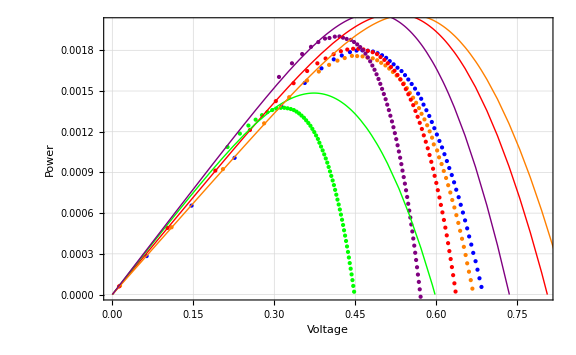

```mathematica
Show[powerplot, Plot[-V(dark80fit - 0.00445),{V,0,1},PlotRange-> {0,0.003},PlotStyle -> {Blue,Thick}],Plot[-V(dark188fit - 0.0048),{V,0,1},PlotRange-> {0,0.003},PlotStyle -> {Red,Thick}],Plot[-V(dark296fit - 0.0051),{V,0,1},PlotRange-> {0,0.003},PlotStyle -> {Green,Thick}],Plot[-V(dark134fit - 0.0045),{V,0,1},PlotRange->{0,0.003},PlotStyle -> {Orange,Thick}],
Plot[-V(dark242fit - 0.0052),{V,0,1},PlotRange-> {0,0.003},PlotStyle -> {Purple,Thick}]]
```

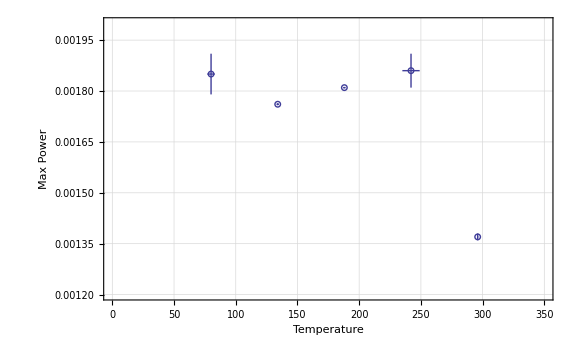

```mathematica
ErrorListPlot[{
{{80,0.00185},ErrorBar[3,0.00006]},
{{134,0.001761},ErrorBar[1,0.000003]},
{{188,0.001810},ErrorBar[1,0.000002]},
{{242,0.00186},ErrorBar[7,0.00005]},
{{296,0.00137},ErrorBar[0.5,0.00001]}
}, ImageSize -> Large, Frame -> True, FrameLabel -> {"Temperature","Max Power"}, GridLines-> Automatic, GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{0,350},{0.0012,0.002}},PlotMarkers -> {m1,.0001}]
```

```mathematica
dataone = {{1/80,-79.49},{1/134,-49.558},{1/188,-35.742},{1/242,-27.854},{1/296,-18.238}};errorone = {-19.87,-12.389,8.935,-6.964,-4.559};
```

```mathematica
NonlinearModelFit[dataone,-a/(8.6173324*10^-5)*x +b,{a,b},{x},Weights->1/errorone^2,VarianceEstimatorFunction->(1&)][{"BestFit","ParameterTable"}]
```

{4.1564-7092.46 x, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.611181 | 0.160161 | 3.81603 | 0.0316583
b | 4.1564 | 8.77766 | 0.47352 | 0.668168}

```mathematica
datatwo = {{1/80,-38.4507},{1/134,-25.68511},{1/188,-20.2568},{1/242,-17.1679},{1/296,-13.28488}};errortwo = {-9.612,-6.4212,-5.0633,-4.2919,-3.32122};
```

```mathematica
NonlinearModelFit[datatwo,-a/(2* 8.6173324*10^-5)*x +b,{a,b},{x},Weights->1/errortwo^2,VarianceEstimatorFunction->(1&)][{"BestFit","ParameterTable"}]
```

{-4.64781-2795.63 x, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.481818 | 0.169688 | 2.83944 | 0.0656771
b | -4.64781 | 5.19899 | -0.893983 | 0.437201}

```mathematica
Manipulate[Plot[-(1/(Rs (1. Rs+1. Rsh))(1. Il Rs Rsh-1. Rs V+n (-0.00008625000000000001 Rs-0.00008625000000000001 Rsh) T ProductLog[(11594.202898550724 ⅇ^((11594.202898550724 Il Rs Rsh+11594.202898550724 Rsh V)/(n Rs T+n Rsh T)) Io Rs Rsh)/(1. n Rs T+1. n Rsh T)])),{V,-1,1},PlotRange-> {-.005,.005}], {Il, 0,.01}, {Rs,1,100}, {Rsh, 1000,10000},{n,1,2},{Io,10^-40,10^-5},{T,80,300}]
```